```mathematica
circle=Circle[{0,0},1]
```

Circle[{0,0},1]



```mathematica
p1=Graphics[Circle[{0,0},1]]
```

```mathematica
func=Sin[x]Sin[y]
```

Sin[x] Sin[y]

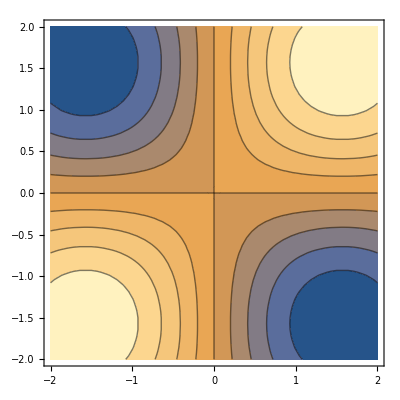

```mathematica
p2=ContourPlot[func,{x,-2,2},{y,-2,2}]
```

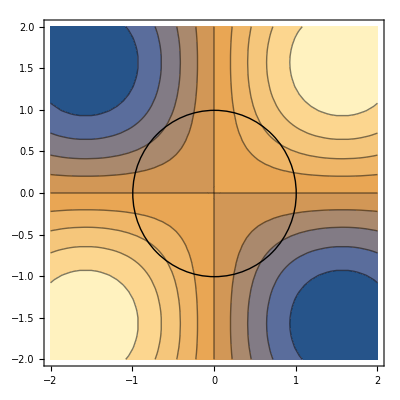

```mathematica
Show[p2,p1]
```

```mathematica
light = FullSimplify[Integrate[func,{x,y}∈Circle[]]]
```

∫_({x,y}∈Circle[{0,0}]) Sin[x] Sin[y]

```mathematica
Evaluate[light]
```

∫_({x,y}∈Circle[{0,0}]) Sin[x] Sin[y]

```mathematica
FullSimplify[Solve[(x-m)/(y-n)==(n-b)/(m-a)&&d==Sqrt[(x-m)^2+(y-n)^2],{x,y}]]
```

{{x→1/((a-m) ((a-m)^2+(b-n)^2))(a^3 m-3 a^2 m^2+b √(d^2 (a-m)^2 ((a-m)^2+(b-n)^2))-m^2 (m^2+(b-n)^2)+a m (3 m^2+(b-n)^2)-√(d^2 (a-m)^2 ((a-m)^2+(b-n)^2)) n),y→(d^2 (a-m)^2)/(√(d^2 (a-m)^2 ((a-m)^2+(b-n)^2)))+n},{x→1/((a-m) ((a-m)^2+(b-n)^2))(a^3 m-3 a^2 m^2-b √(d^2 (a-m)^2 ((a-m)^2+(b-n)^2))-m^2 (m^2+(b-n)^2)+a m (3 m^2+(b-n)^2)+√(d^2 (a-m)^2 ((a-m)^2+(b-n)^2)) n),y→-(d^2 (a-m)^2)/(√(d^2 (a-m)^2 ((a-m)^2+(b-n)^2)))+n}}